#### Градиентный спуск для одной переменной

```mathematica
data=Table[{i,RandomReal[3]*3+i+5},{i,1,30}];
```

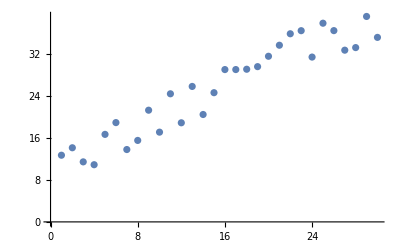

```mathematica
ListPlot[data]
```

```mathematica
LinearModelFit[Y,x,x]
```

FittedModel[9.26797+1.04646 x]

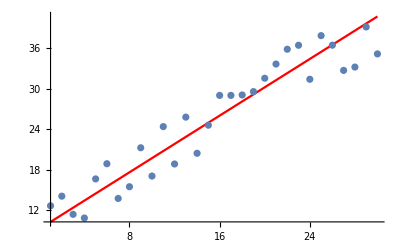

```mathematica
Show[Plot[9.267973674261254+1.0464626524494172 x,{x,1,30},PlotStyle->Red],ListPlot[data]]
```

```mathematica
Y=data[[All,2]];
X=Transpose[{data[[All,1]],ConstantArray[1,30]}];
```

```mathematica
Clear[f]
f[a_,b_]:=Total[(Y-X.{a,b})^2]
```

```mathematica
grada=D[Total[(Y-X.{a,b})^2],a];
gradb=D[Total[(Y-X.{a,b})^2],b];
```

```mathematica
Clear[df]
df[a0_,b0_]:={D[Total[(Y-X.{a,b})^2],a],D[Total[(Y-X.{a,b})^2],b]}/.{a->a0,b->b0};
```

```mathematica
w0={0,0};
res={};
λ=0.00001;
```

```mathematica
While[
AppendTo[res,w0];
w1=w0-λ df@@w0;
Norm[w1-w0]>0.0001,
w0=w1
]
```

```mathematica
Dynamic[w0]
```

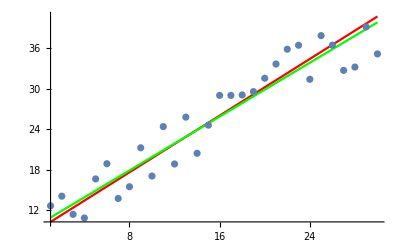

```mathematica
Show[Plot[9.267973674261254+1.0464626524494172 x,{x,1,30},PlotStyle->Red],Plot[w0[[2]]+w0[[1]] x,{x,1,30},PlotStyle->Green],ListPlot[data]]
```

#### Стохастический градиентный спуск

```mathematica
Y=data[[All,2]];
X=Transpose[{data[[All,1]],ConstantArray[1,30]}];
```

```mathematica
Clear[f]
f[a_,b_]:=Total[(Y-X.{a,b})^2]
```

```mathematica
Clear[df]
df[a0_,b0_]:=With[{point=RandomInteger[{1,Length@data}]},
{D[(Y[[point]]-X[[point]].{a,b})^2,a],D[(Y[[point]]-X[[point]].{a,b})^2,b]}/.{a->a0,b->b0}];
```

```mathematica
w0={0,0};
res={};
λ=0.00001;
```

```mathematica
While[
AppendTo[res,w0];
w1=w0-λ df@@w0;
Norm[w1-w0]>0.0001,
w0=w1
]
```

```mathematica
Dynamic[w0]
```

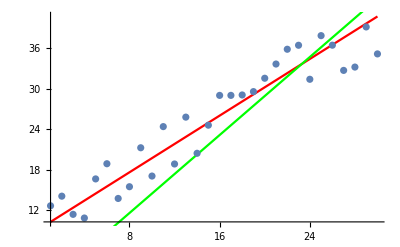

```mathematica
Show[Plot[9.267973674261254+1.0464626524494172 x,{x,1,30},PlotStyle->Red],Plot[w0[[2]]+w0[[1]] x,{x,1,30},PlotStyle->Green],ListPlot[data]]
```

```mathematica
D[(y-a x + b )^2,a]
```

-2 x (b-a x+y)

```mathematica
D[(y-a x + b )^2,b]
```

2 (b-a x+y)